# Speed of sound calculation from P(μ)

## Authors: Christian Drischler, Alexandra Semposki, Daniel Phillips Last edited: 15 January 2024

## Quantities from QCD

To begin, we define the quantities from QCD that we will need to compute the speed of sound. 
First is the QCD beta function. We only need this up to one loop, since we carry out the calculation only up to O(α_S^2).

```mathematica
RGEq[alphas_]:=-b[0] alphas^2
```

According to the PDG we have  (for N_C=3, for which case we have C_A=3):

```mathematica
b[0]=(33 -2 Nf)/(12 π)
```

(33-2 Nf)/(12 π)

(Note that this is not the same b[0] as Gorda et al.’s.) 
Now we define the pressure up to O(α_S^2). For this we use the expression from Gorda et al., arXiv:2307.08734.

```mathematica
P[μ_]:=Pfree[μ]*(1+alphas[2 X μ]/π*a[11]+Nf/π^2*alphas[2 X μ]^2(a[21]*Log[(Nf alphas[2 X μ])/π]+a[22]*Log[Λbar[μ,X]/(2 μ)]+ a[23]))
```

where the quantity Λbar is taken to be proportional to

```mathematica
Λbar[μ_,X_]:=2  X μ
```

The parameter X expresses the relationship between the chemical potential μ and the scale at which α_S is to be evaluated. On theoretical grounds (see Kurkela, Romatschke, Vuorinen, Phys. Rev. D 81, 105021 (2010)) we take X=1. Variation between X=1/2 and X=2 provides some assessment of scale uncertainty.

The coefficients in the expression for P(μ) take the values (for N_C=3):

```mathematica
a[11]=-2; a[21]=-1;a[22]=(2 π b[0])/Nf a[11];a[23]=8*(1/3*(11/6-π^2/8-5/4 Log[2]+Log[2]^2-3/16 δ)-415/(192 Nf)-51/(64*9 Nf));
```

## Speed of sound to first order

Now we are ready to compute the speed of sound to second order in α_S. The first derivative is:

```mathematica
D[P[μ],μ]
```

Pfree[μ] (-(4 X alphas'[2 X μ])/π-(2 Nf X alphas[2 X μ] alphas'[2 X μ])/π^2+(4 Nf X alphas[2 X μ] (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]) alphas'[2 X μ])/π^2)+(1-(2 alphas[2 X μ])/π+(Nf alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/π^2) Pfree'[μ]

We could use the beta function already now, but we wait to do that. Instead we just define:

```mathematica
deriv1[μ_] := D[P[μ],μ]
```

Now we take the second derivative of this result for the pressure. In this quantity we replace the second derivative of α_S with zero, since it is beyond the order of our calculation, and we again use the beta function to evaluate the first derivative of α_S.

```mathematica
deriv2[μ_] :=ReplaceAll[D[deriv1[μ], μ], {alphas''[2 μ X] -> 0,alphas'[2 X μ] ->2/μ RGEq[alphas[2 X μ]] }]
```

yielding:

```mathematica
deriv2[μ]
```

(-((33-2 Nf)^2 Nf X^2 alphas[2 X μ]^4)/(3 π^4 μ^2)+(2 (33-2 Nf)^2 Nf X^2 alphas[2 X μ]^4 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/(9 π^4 μ^2)) Pfree[μ]+2 ((2 (33-2 Nf) X alphas[2 X μ]^2)/(3 π^2 μ)+((33-2 Nf) Nf X alphas[2 X μ]^3)/(3 π^3 μ)-(2 (33-2 Nf) Nf X alphas[2 X μ]^3 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/(3 π^3 μ)) Pfree'[μ]+(1-(2 alphas[2 X μ])/π+(Nf alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/π^2) Pfree''[μ]

Finally, we define Pfree[μ]

```mathematica
Pfree[μ_] := (Nf  μ^4)/(4 π^2)
```

and make the RG replacement in the numerator:

```mathematica
numerator[μ_]:=ReplaceAll[deriv1[μ],{alphas'[2 X μ] ->2/μ RGEq[alphas[2 X μ]] }]
```

so  we  can compute the speed of sound:

```mathematica
soundspeed[μ_] := numerator[μ] / (deriv2[μ] * μ)
```

```mathematica
Series[soundspeed[μ], {alphas[2 X μ], 0, 2}]//FullSimplify
```

1/3+(5 (-33+2 Nf) X alphas[2 X μ]^2)/(54 π^2)+O[alphas[2 X μ]]^3

This demonstrates our claim that there is no O(α_S) contribution to the speed of sound. 
And, since

```mathematica
N[(5 * (-33 + 2 * Nf))/(54 π^2)/.{Nf->2,δ->-0.85638, X->1}]
```

-0.272066

is  a  negative number, it means that the approach to the asymptotic value of 1/3 is from below.

Note  that this coefficient is somewhat small, if the expansion parameter is α_S, but it is very natural if the expansion parameter is α_S/π^2.

## Taking derivatives etc. for KLW purposes

Here we implement and evaluate the formulae from Appendix A of our paper.

### Perturbative expansion of μ

First, the perturbative expansion of the chemical potential that produces a given density. If μ0 is the chemical potential that produces that density in the free Fermi gas, then the first order correction is (see Eq. (A4)):

```mathematica
μ1=-a[11]/π*D[Pfree[μ],μ]/D[D[Pfree[μ],μ],μ]*alphas[2 X μ]
```

(2 μ alphas[2 X μ])/(3 π)

The second-order correction has several pieces, see Eq. (A5), where we take c_0=1.

```mathematica
μ21=-μ1^2/2  D[Pfree[μ],{μ,3}]/D[Pfree[μ],{μ,2}]
```

-(4 μ alphas[2 X μ]^2)/(9 π^2)

```mathematica
μ22=-μ1 a[11]/π alphas[2 X μ]
```

(4 μ alphas[2 X μ]^2)/(3 π^2)

Taken together, these reproduce the first term in Eq. (A6):

```mathematica
μ21+μ22
```

```mathematica
(8 μ alphas[2 X μ]^2)/(9 π^2)
```

(8 μ alphas[2 X μ]^2)/(9 π^2)

The next term in Eq. (A5) involves the beta function of QCD:

```mathematica
μ23=-a[11]/π D[alphas[2 X μ],μ] Pfree[μ]/D[Pfree[μ],{μ,2}]
```

(X μ^2 alphas'[2 X μ])/(3 π)

This agrees with the third term in Eq. (A6), up to a factor of 2X, which comes from applying the chain rule when taking the derivative of α_S. If we use the beta function defined above we find:

```mathematica
ReplaceAll[%,{alphas'[2 X μ] ->2/μ RGEq[alphas[2 X μ]] }]
```

-((33-2 Nf) X μ alphas[2 X μ]^2)/(18 π^2)

The next term in Eq. (A4) involves the derivative of the coefficient of the second-order term with respect to μ. But, that coefficient depends on μ only through α_S, and so the derivative of what is called c_2(μ) in the notes is a term of order α_S^3.

```mathematica
μ24=-D[Nf/π^2(a[21]*Log[(Nf alphas[2 X μ])/π]+a[22]*Log[Λbar[μ,X]/(2 μ)]+ a[23]),μ] alphas[2 X μ]^2 Pfree[μ]/D[Pfree[μ],{μ,2}]
```

(Nf X μ^2 alphas[2 X μ] alphas'[2 X μ])/(6 π^2)

It can therefore be ignored.

The last term imitates the structure of the μ1 term above, but this time with the (more complicated) second-order coefficient instead of the first-order one:

```mathematica
μ25=-Nf/π^2(a[21]*Log[(Nf alphas[2 X μ])/π]+a[22]*Log[Λbar[μ,X]/(2 μ)]+ a[23])alphas[2 X μ]^2 D[Pfree[μ],μ]/D[D[Pfree[μ],μ],μ]
```

-(Nf μ alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/(3 π^2)

where the expression in brackets, together with the factor of Nf/π^2 can be understood as the coefficient c_2(μ), and so this agrees with the final term in Eq. (A6).

Overall, then we have:

```mathematica
μ2=μ21 + μ22 + μ23 + μ25
```

(8 μ alphas[2 X μ]^2)/(9 π^2)-(Nf μ alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/(3 π^2)+(X μ^2 alphas'[2 X μ])/(3 π)

### Perturbative expansion of P(n), using perturbative expansion of μ and the formula for P(μ)

Now we insert the perturbative expansion of μ into the order-by-order expression for P(μ)/PFG(μ). The first-order term is:

```mathematica
p1=μ1 D[Pfree[μ],μ]/Pfree[μ]+a[11]/π alphas[2 X μ]
```

(2 alphas[2 X μ])/(3 π)

This agrees with the first-order term in Eq. (A10).

Now we need to collect all the second-order terms. They are, in the order they appear in (A9):

```mathematica
p2=μ2 D[Pfree[μ],μ]/Pfree[μ]+μ1^2/2 D[Pfree[μ],{μ,2}]/Pfree[μ]+μ1*a[11]/π alphas[2 X μ] D[Pfree[μ],μ]/Pfree[μ]+Nf/π^2*alphas[2 X μ]^2(a[21]*Log[(Nf alphas[2 X μ])/π]+a[22]*Log[Λbar[μ,X]/(2 μ)]+ a[23])
```

-(8 alphas[2 X μ]^2)/(3 π^2)+(Nf alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/π^2+(4 ((8 μ alphas[2 X μ]^2)/(9 π^2)-(Nf μ alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/(3 π^2)+(X μ^2 alphas'[2 X μ])/(3 π)))/μ

where we have plugged in for c_2(μ). Now we are going to, um, un-plug-in, in order to compare with Alexandra’s expression:

```mathematica
ReplaceAll[%,{Nf/π^2(a[21]*Log[(Nf alphas[2 X μ])/π]+a[22]*Log[Λbar[μ,X]/(2 μ)]+ a[23])->c2}]
```

c2 alphas[2 X μ]^2-(8 alphas[2 X μ]^2)/(3 π^2)+(4 (-1/3 c2 μ alphas[2 X μ]^2+(8 μ alphas[2 X μ]^2)/(9 π^2)+(X μ^2 alphas'[2 X μ])/(3 π)))/μ

```mathematica
Simplify[%]
```

```mathematica
((8-3 c2 π^2) alphas[2 X μ]^2+12 π X μ alphas'[2 X μ])/(9 π^2)
```

((8-3 c2 π^2) alphas[2 X μ]^2+12 π X μ alphas'[2 X μ])/(9 π^2)

where it should be noted that we have chosen not to retain the last term in (A10), involving the derivative of c_2 with respect to μ.

The coefficients of the other two terms agree with (A10).

### Full result for p2

Of course, for p2 in full glory we write out c2 in full, and we also use the RGE to replace the derivative of α_S

```mathematica
ReplaceAll[p2,{alphas'[2 X μ] ->2/μ RGEq[alphas[2 X μ]] }]
```

-(8 alphas[2 X μ]^2)/(3 π^2)+(4 ((8 μ alphas[2 X μ]^2)/(9 π^2)-((33-2 Nf) X μ alphas[2 X μ]^2)/(18 π^2)-(Nf μ alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/(3 π^2)))/μ+(Nf alphas[2 X μ]^2 (8 (-9/(4 Nf)+1/3 (11/6-π^2/8-(3 δ)/16-(5 Log[2])/4+Log[2]^2))-((33-2 Nf) Log[X])/(3 Nf)-Log[(Nf alphas[2 X μ])/π]))/π^2

```mathematica
Simplify[%]
```

(alphas[2 X μ]^2 (372-88 Nf+6 Nf π^2-396 X+24 Nf X+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(Nf alphas[2 X μ])/π]))/(54 π^2)

```mathematica
%/.{X->1,Nf->2,δ->-0.85638}
```

```mathematica
(alphas[2 μ]^2 (-11.925414855881598+36 Log[(2 alphas[2 μ])/π]))/(54 π^2)
```

(alphas[2 μ]^2 (-11.9254+36 Log[(2 alphas[2 μ])/π]))/(54 π^2)

```mathematica
(alphas[2 μ]^2 (162.07458514411843+36 Log[(2 alphas[2 μ])/π]))/(54 π^2)
```

(alphas[2 μ]^2 (162.075+36 Log[(2 alphas[2 μ])/π]))/(54 π^2)

In order to plot this I import my result for α_S, with the sub-leading correction to the beta function, from another notebook. Note that this is not strictly consistent with the expansion we are using here, but we need to do it this way in order to be able to use a single value of Λ_QCD throughout the calculuation, and not have that parameter different at each order.

```mathematica
alphaS2[mu_,X_]:=(4 π)/(β0 L[2*X*mu])(1-(2β1)/β0^2*Log[L[2*X*mu]]/L[2*X*mu] )
```

```mathematica
L[Q_]:=Log[(Q)^2/LambdaQCD^2]
```

```mathematica
LambdaQCD=0.38;
```

```mathematica
β0=(11 * 3  - 2 * Nf)/3;β1=(17/3)*9 - (4/3)*Nf - (5/3) * 3 * Nf;
```

With α_S defined in this way we can plot the α_S^2 coefficient of the pressure (with p_FGdivided out):

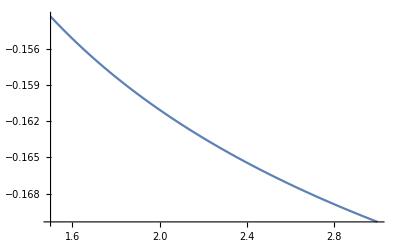

```mathematica
Plot[(-11.925414855881598+36 Log[(2 alphaS2[μ,X])/π])/(54 π^2)/.{X->1,Nf->2,δ->-0.85638},{μ,1.5,3}]
```

It is negative, which will counter-balance the positive correction at O(α_S).

### Full result for p/p_FG

In fact, we can now plot p/p_FG. Copy-pasting the above results for p1 and p2, but making sure to use the full α_S we define this ratio as:

```mathematica
pofnpQCD[μFG_]:=1 + 2/(3 π) alphaS2[μFG,X] + (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(Nf alphaS2[μFG,X])/π])/(54 π^2)alphaS2[μFG,X]^2
```

Although this is written as a function of μ, this is understood to be the Fermi-gas value of μ that gives the n of interest.

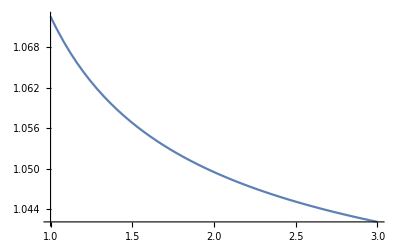

```mathematica
Plot[pofnpQCD[μFG]/.{X->1,Nf->2,δ->-0.85638},{μFG,1,3}]
```

### Speed of sound

Emboldened, we will try to compute the speed of sound from these result. For this we use the representation c_S^-2=d(log n)/d(log μ). 
(N.B. This calculation is ill-conceived, because the p I am differentiating is a function of n, but I am treating it as a function of μ.)
First we get the number density, by taking a derivative:

```mathematica
n[μ_]:=D[Pfree[μ]*pofnpQCD[μ],μ]
```

And  now we can get the speed of sound. Because we want to plot it, we have to do this in a messy way:

```mathematica
μ D[Log[n[μ]],μ]
```

(μ (1/(4 π^2)Nf μ^4 ((0.275864 (9.84555/(μ^2 Log[27.7008 X^2 μ^2]^3)+1.64092/(μ^2 Log[27.7008 X^2 μ^2]^2)-(6.5637 Log[Log[27.7008 X^2 μ^2]])/(μ^2 Log[27.7008 X^2 μ^2]^3)-(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ^2 Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(1.10346 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/(μ Log[27.7008 X^2 μ^2]^2)+(2.20691 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ^2 Log[27.7008 X^2 μ^2]^3)+(0.551728 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ^2 Log[27.7008 X^2 μ^2]^2)+1/Log[27.7008 X^2 μ^2]0.137932 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) ((0.413796 Nf (9.84555/(μ^2 Log[27.7008 X^2 μ^2]^3)+1.64092/(μ^2 Log[27.7008 X^2 μ^2]^2)-(6.5637 Log[Log[27.7008 X^2 μ^2]])/(μ^2 Log[27.7008 X^2 μ^2]^3)-(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ^2 Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(1.65518 Nf (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/(μ Log[27.7008 X^2 μ^2]^2)+(3.31037 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ^2 Log[27.7008 X^2 μ^2]^3)+(0.827592 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ^2 Log[27.7008 X^2 μ^2]^2))+(0.413796 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)) ((0.413796 Nf (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(0.827592 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(0.827592 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) ((0.413796 Nf (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(0.827592 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ Log[27.7008 X^2 μ^2]^2)))/(μ Log[27.7008 X^2 μ^2]^2)+1/(Log[27.7008 X^2 μ^2]^2)0.00634174 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2))^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]])+1/(Log[27.7008 X^2 μ^2]^2)0.00634174 (9.84555/(μ^2 Log[27.7008 X^2 μ^2]^3)+1.64092/(μ^2 Log[27.7008 X^2 μ^2]^2)-(6.5637 Log[Log[27.7008 X^2 μ^2]])/(μ^2 Log[27.7008 X^2 μ^2]^3)-(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ^2 Log[27.7008 X^2 μ^2]^2)) (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]])-1/(μ Log[27.7008 X^2 μ^2]^3)0.050734 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)) (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]])+1/(μ^2 Log[27.7008 X^2 μ^2]^4)0.0761009 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]])+1/(μ^2 Log[27.7008 X^2 μ^2]^3)0.0126835 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]]))+1/π^2 2 Nf μ^3 ((0.275864 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(0.551728 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ Log[27.7008 X^2 μ^2]^2)+(0.137932 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) ((0.413796 Nf (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(0.827592 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]+1/(Log[27.7008 X^2 μ^2]^2)0.00634174 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)) (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]])-1/(μ Log[27.7008 X^2 μ^2]^3)0.0126835 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]]))+1/π^2 3 Nf μ^2 (1+(0.275864 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]+1/(Log[27.7008 X^2 μ^2]^2)0.00317087 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]]))))/(1/(4 π^2)Nf μ^4 ((0.275864 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(0.551728 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ Log[27.7008 X^2 μ^2]^2)+(0.137932 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) ((0.413796 Nf (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]-(0.827592 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/(μ Log[27.7008 X^2 μ^2]^2)))/Log[27.7008 X^2 μ^2]+1/(Log[27.7008 X^2 μ^2]^2)0.00634174 (-1.64092/(μ Log[27.7008 X^2 μ^2]^2)+(1.64092 Log[Log[27.7008 X^2 μ^2]])/(μ Log[27.7008 X^2 μ^2]^2)) (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]])-(0.0126835 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]]))/(μ Log[27.7008 X^2 μ^2]^3))+1/π^2 Nf μ^3 (1+(0.275864 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]+1/(Log[27.7008 X^2 μ^2]^2)0.00317087 (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413796 Nf (1-(0.820462 Log[Log[27.7008 X^2 μ^2]])/Log[27.7008 X^2 μ^2]))/Log[27.7008 X^2 μ^2]])))

```mathematica
csminus2[μ_]:=(μ (1/(4 π^2)Nf μ^4 ((0.2758639714756653 (9.845549355503808/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)+1.640924892583968/(μ^2 Log[27.700831024930746 X^2 μ^2]^2)-(6.563699570335872 Log[Log[27.700831024930746 X^2 μ^2]])/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)-(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ^2 Log[27.700831024930746 X^2 μ^2]^2)))/Log[27.700831024930746 X^2 μ^2]-(1.1034558859026613 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/(μ Log[27.700831024930746 X^2 μ^2]^2)+(2.2069117718053226 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)+(0.5517279429513307 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ^2 Log[27.700831024930746 X^2 μ^2]^2)+1/Log[27.700831024930746 X^2 μ^2] 0.13793198573783266 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) (1/Log[27.700831024930746 X^2 μ^2] 0.413795957213498 Nf (9.845549355503808/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)+1.640924892583968/(μ^2 Log[27.700831024930746 X^2 μ^2]^2)-(6.563699570335872 Log[Log[27.700831024930746 X^2 μ^2]])/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)-(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ^2 Log[27.700831024930746 X^2 μ^2]^2))-(1.655183828853992 Nf (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/(μ Log[27.700831024930746 X^2 μ^2]^2)+(3.310367657707984 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)+(0.827591914426996 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ^2 Log[27.700831024930746 X^2 μ^2]^2))+1/Log[27.700831024930746 X^2 μ^2] 0.413795957213498 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)) ((0.413795957213498 Nf (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/Log[27.700831024930746 X^2 μ^2]-(0.827591914426996 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ Log[27.700831024930746 X^2 μ^2]^2))-1/(μ Log[27.700831024930746 X^2 μ^2]^2)0.827591914426996 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) ((0.413795957213498 Nf (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/Log[27.700831024930746 X^2 μ^2]-(0.827591914426996 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ Log[27.700831024930746 X^2 μ^2]^2))+1/(Log[27.700831024930746 X^2 μ^2]^2)0.0063417442298605575 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2))^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]])+1/(Log[27.700831024930746 X^2 μ^2]^2)0.0063417442298605575 (9.845549355503808/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)+1.640924892583968/(μ^2 Log[27.700831024930746 X^2 μ^2]^2)-(6.563699570335872 Log[Log[27.700831024930746 X^2 μ^2]])/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)-(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ^2 Log[27.700831024930746 X^2 μ^2]^2)) (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]])-1/(μ Log[27.700831024930746 X^2 μ^2]^3)0.05073395383888446 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)) (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]])+1/(μ^2 Log[27.700831024930746 X^2 μ^2]^4)0.07610093075832669 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]])+1/(μ^2 Log[27.700831024930746 X^2 μ^2]^3)0.012683488459721115 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]]))+1/π^2 2 Nf μ^3 ((0.2758639714756653 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/Log[27.700831024930746 X^2 μ^2]-(0.5517279429513307 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ Log[27.700831024930746 X^2 μ^2]^2)+1/Log[27.700831024930746 X^2 μ^2] 0.13793198573783266 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) ((0.413795957213498 Nf (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/Log[27.700831024930746 X^2 μ^2]-(0.827591914426996 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ Log[27.700831024930746 X^2 μ^2]^2))+1/(Log[27.700831024930746 X^2 μ^2]^2)0.0063417442298605575 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)) (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]])-1/(μ Log[27.700831024930746 X^2 μ^2]^3)0.012683488459721115 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]]))+1/π^2 3 Nf μ^2 (1+(0.2758639714756653 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]+1/(Log[27.700831024930746 X^2 μ^2]^2)0.0031708721149302788 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]]))))/(1/(4 π^2)Nf μ^4 ((0.2758639714756653 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/Log[27.700831024930746 X^2 μ^2]-(0.5517279429513307 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ Log[27.700831024930746 X^2 μ^2]^2)+1/Log[27.700831024930746 X^2 μ^2] 0.13793198573783266 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) ((0.413795957213498 Nf (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)))/Log[27.700831024930746 X^2 μ^2]-(0.827591914426996 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/(μ Log[27.700831024930746 X^2 μ^2]^2))+1/(Log[27.700831024930746 X^2 μ^2]^2)0.0063417442298605575 (-1.640924892583968/(μ Log[27.700831024930746 X^2 μ^2]^2)+(1.640924892583968 Log[Log[27.700831024930746 X^2 μ^2]])/(μ Log[27.700831024930746 X^2 μ^2]^2)) (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]) (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]])-1/(μ Log[27.700831024930746 X^2 μ^2]^3)0.012683488459721115 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]]))+1/π^2 Nf μ^3 (1+(0.2758639714756653 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]+1/(Log[27.700831024930746 X^2 μ^2]^2)0.0031708721149302788 (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2])^2 (174-76 Nf+6 Nf π^2+9 Nf δ+60 Nf Log[2]-48 Nf Log[2]^2-6 (-33+2 Nf) Log[X]+18 Nf Log[(0.413795957213498 Nf (1-(0.820462446291984 Log[Log[27.700831024930746 X^2 μ^2]])/Log[27.700831024930746 X^2 μ^2]))/Log[27.700831024930746 X^2 μ^2]])))
```

So finally we plot the speed of sound squared, and find it approaches 1/3 from above. But it is very close to 1/3 already at 1 GeV.

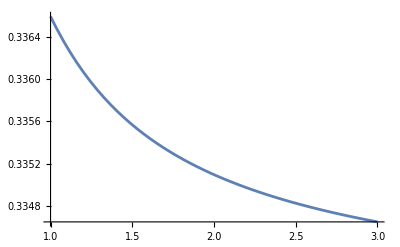

```mathematica
Plot[1/csminus2[μ]/.{X->1,Nf->2,δ->-0.85638},{μ,1,3}]
```